```mathematica
baseu = Import["D:\\YanXiao\\Github\\Divergence-free_Wavelet\\mathematica\\uelocity.txt","Table"];basev = Import["D:\\YanXiao\\Github\\Divergence-free_Wavelet\\mathematica\\velocity.txt","Table"];
```

```mathematica
modu = Import["D:\\YanXiao\\Github\\Divergence-free_Wavelet\\mathematica\\lastu.txt","Table"];modv = Import["D:\\YanXiao\\Github\\Divergence-free_Wavelet\\mathematica\\lastv.txt","Table"];
```

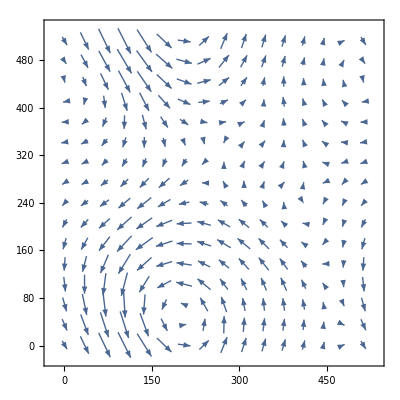

```mathematica
ListVectorPlot[Table[{baseu[[y,x]],basev[[y,x]]},{x,512},{y,512}],VectorPoints->16]
```

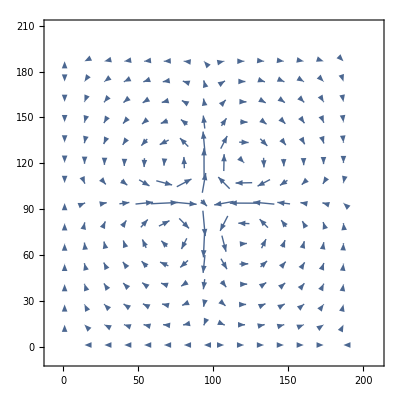

```mathematica
ListVectorPlot[Table[{modu[[y,x]],modv[[y,x]]},{x,200},{y,200}],VectorPoints->16]
```